# Dimensionality Reduction

## Chapter 1: Make data simple

```mathematica
oxyYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSoxy_yes_signal.mat"];
numSamplesOxyYes = Dimensions[oxyYesMatlab][[3]];
oxyYesRaw =  Table[Transpose[oxyYesMatlab[[1,1,x]]],{x,numSamplesOxyYes}];

oxyNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/NIRSoxy_no_signal.mat"];
numSamplesOxyNo = Dimensions[oxyNoMatlab][[3]];
oxyNoRaw =  Table[Transpose[oxyNoMatlab[[1,1,x]]],{x,numSamplesOxyNo}];
```

```mathematica
oxyYesRaw80={};
If[Dimensions[oxyYesRaw[[#]]][[2]]==81,AppendTo[oxyYesRaw80,Transpose@Drop[Transpose@oxyYesRaw[[#]],-1]], AppendTo[oxyYesRaw80,oxyYesRaw[[#]]]]&/@Range[numSamplesOxyYes];
```

```mathematica
oxyNoRaw80={};
If[Dimensions[oxyNoRaw[[#]]][[2]]==81,AppendTo[oxyNoRaw80,Transpose@Drop[Transpose@oxyNoRaw[[#]],-1]], AppendTo[oxyNoRaw80,oxyNoRaw[[#]]]]&/@Range[numSamplesOxyNo];
```

```mathematica
Dimensions[oxyNoRaw80]
```

{30,15,80}

```mathematica
Dimensions[oxyYesRaw80]
```

{30,15,80}

```mathematica
OxyNo80ToBeReduced=Transpose@Fold[Join[#1,#2]&,Transpose@oxyNoRaw80[[1]],Array[Transpose@oxyNoRaw80[[#]]&,numSamplesOxyNo-1,{2,numSamplesOxyNo}]];
```

```mathematica
Dimensions[%]
```

{15,2400}

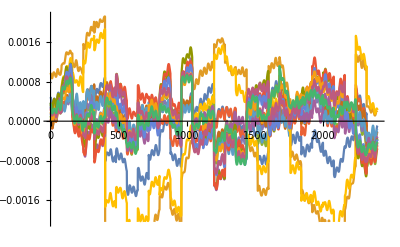

```mathematica
ListLinePlot[OxyNo80ToBeReduced]
```

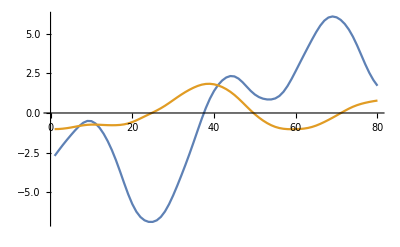

```mathematica
DimensionReduce[Transpose@oxyYesRaw80[[5]],2,Method->"PrincipalComponentsAnalysis"]//Transpose//ListLinePlot
```

```mathematica
reducedOxyNo80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@oxyNoRaw80;
```

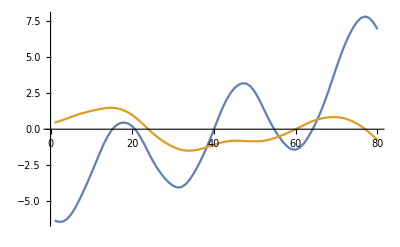

```mathematica
ListLinePlot[reducedOxyNo80[[3]]]
```

```mathematica
reducedOxyYes80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@oxyYesRaw80;
```

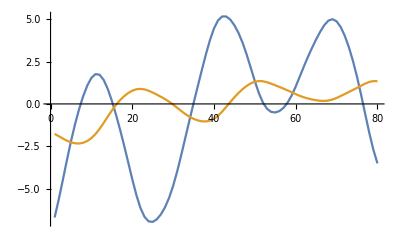

```mathematica
ListLinePlot[reducedOxyYes80[[3]]]
```

# HMM

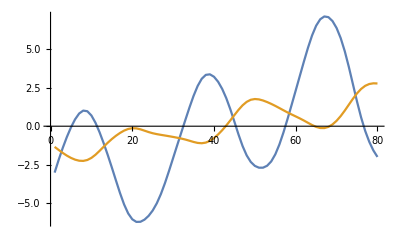

```mathematica
ListLinePlot[reducedOxyYes80[[1]]]
```

```mathematica
hiddenProcess = 2
```

2

```mathematica
hmmYes[i_Integer] := EstimatedProcess[reducedOxyYes80[[i]],HiddenMarkovProcess[hiddenProcess,"Gaussian"],ProcessEstimator->"MaximumLikelihood"]
```

```mathematica
hmmNo= EstimatedProcess[reducedOxyNo80[[1]],HiddenMarkovProcess[hiddenProcess,"Gaussian"],ProcessEstimator->"MaximumLikelihood"]
```

HiddenMarkovProcess[{0.00823848,0.991762},{{0.986651,0.013349},{0.0277829,0.972217}},{NormalDistribution[-0.107609,0.686689],NormalDistribution[0.119656,3.79501]}]

```mathematica
Clear[hmmNo]
```

```mathematica
Clear[hmmNo]
```

```mathematica
pi = hmmNo[[1]]//Column
transMatrix = hmmNo[[2]]//Grid
mu = Table[hmmNo[[3]][[x]][[1]],{x,hiddenProcess}]
sigma = Table[hmmNo[[3]][[x]][[2]],{x,hiddenProcess}]
```

0.00823848
0.991762

0.986651 | 0.013349
0.0277829 | 0.972217

{-0.107609,0.119656}

{0.686689,3.79501}

```mathematica
pYes[k_]:=Likelihood[hmmYes[1],reducedOxyYes80[[k]]]
```

```mathematica
pNo[k_]:=Likelihood[hmmNo[1],reducedOxyYes80[[k]]]
```

```mathematica
Array[pNo,2]
```

{1.04378×10^-150,1.78662×10^-139}

```mathematica
gamma1[r_]:=
```

```mathematica
Table[LogLikelihood[hmmYes,reducedOxyYes80[[x]]]>LogLikelihood[hmmNo,reducedOxyYes80[[x]]],{x,2,30}]
```

{True,False,False,True,False,False,False,True,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,True,False,True,False,False}

```mathematica
Counts[%28]/30.0
```

<|False→0.833333,True→0.133333|>

```mathematica
Likelihood[hmmYes,reducedOxyYes80[[2]]]
```

3.93583×10^-149

```mathematica
Exp[%]
```

7.58395×10^-147

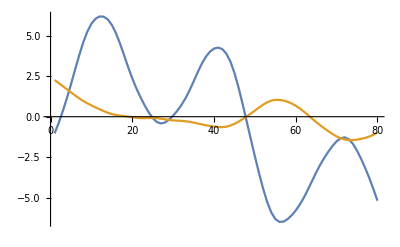

```mathematica
ListLinePlot[reducedOxyNo80[[1]]]
```

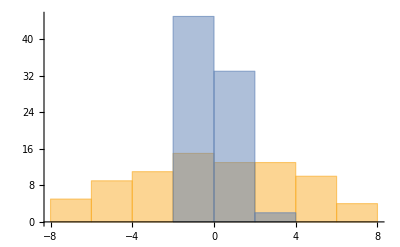

```mathematica
Histogram[reducedOxyNo80[[1]]]
```

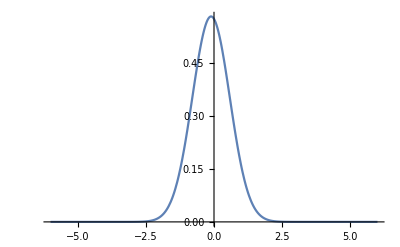

```mathematica
Plot[PDF[hmmNo[[3]][[1]]][x],{x,-6,6}]
```

```mathematica
hmmNo= EstimatedProcess[reducedOxyNo80[[1]],HiddenMarkovProcess[6,"Gaussian"],ProcessEstimator->"MaximumLikelihood"]
```

HiddenMarkovProcess[{0.,4.85963×10^-156,0.49945,1.43492×10^-174,0.50055,1.24963×10^-219},{{1.,6.676×10^-65,2.31517×10^-43,1.53058×10^-164,6.87476×10^-177,3.97543×10^-206},{2.55612×10^-270,1.,2.09633×10^-166,2.47371×10^-105,6.08162×10^-30,1.9818×10^-62},{0.0583446,1.45215×10^-60,0.815242,0.0699107,3.90444×10^-44,0.056503},{4.84751×10^-98,9.81053×10^-40,0.0687125,0.866611,3.07312×10^-65,0.0646763},{1.42832573337581×10^-338,0.0279122,1.92489×10^-140,2.05139×10^-66,0.915469,0.0566192},{1.09926×10^-214,5.30948×10^-24,3.22268×10^-67,0.0997298,0.0671733,0.833097}},{NormalDistribution[-1.26428,0.160447],NormalDistribution[-3.66037,1.84546],NormalDistribution[-0.555943,0.180949],NormalDistribution[-0.10383,0.164057],NormalDistribution[3.52549,1.55119],NormalDistribution[0.753161,0.336516]}]

```mathematica
hmmNo2= EstimatedProcess[reducedOxyNo80[[2]],hmmNo,ProcessEstimator->"MaximumLikelihood"]
```

HiddenMarkovProcess[{0.00823848,0.991762},{{0.986651,0.013349},{0.0277829,0.972217}},{NormalDistribution[-0.107609,0.686689],NormalDistribution[0.119656,3.79501]}]

```mathematica
hmmNo3 = EstimatedProcess[reducedOxyNo80[[3]],hmmNo2,ProcessEstimator->"MaximumLikelihood"]
```

HiddenMarkovProcess[{0.00823848,0.991762},{{0.986651,0.013349},{0.0277829,0.972217}},{NormalDistribution[-0.107609,0.686689],NormalDistribution[0.119656,3.79501]}]

```mathematica
hmmNo==hmmNo3
```

True

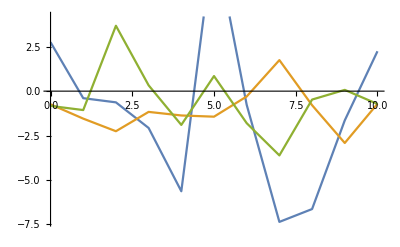

```mathematica
sims=RandomFunction[hmmNo,{0,10},3]//ListLinePlot
```

```mathematica
hmmNoAll = Fold[ EstimatedProcess[reducedOxyNo80[[#]],hmmNo,ProcessEstimator->"MaximumLikelihood"]&,1,{2,3}]
```

```mathematica
hmmNo= EstimatedProcess[reducedOxyNo80[[1,1]],HiddenMarkovProcess[4,"Gaussian"],ProcessEstimator->"MaximumLikelihood"]
```

HiddenMarkovProcess[{3.55472507848603×10^-1274,1.,4.48766×10^-143,1.15394705368317×10^-1151},{{0.934869,8.2711×10^-123,1.76377×10^-266,0.0651307},{1.79676×10^-46,0.861081,0.0926845,0.0462343},{2.72236×10^-151,0.0758294,0.924171,1.07738×10^-69},{0.128838,8.92297×10^-72,1.50466×10^-134,0.871162}},{NormalDistribution[-5.27362,0.939181],NormalDistribution[0.47341,0.861989],NormalDistribution[4.16567,1.2653],NormalDistribution[-2.18243,0.759399]}]

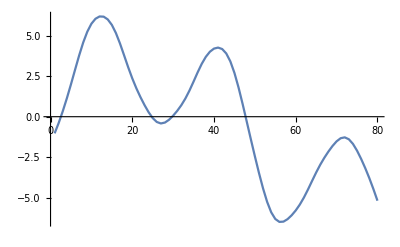

```mathematica
ListLinePlot[reducedOxyNo80[[1,1]]]
```

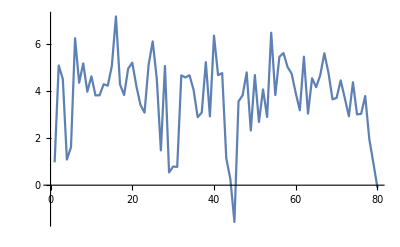

```mathematica
ListLinePlot[RandomFunction[hmmNo,{1,80},1]]
```

```mathematica
hmmNoAllBoscaiolo = Module[{temp,n=2},
temp = EstimatedProcess[reducedOxyNo80[[1]],HiddenMarkovProcess[hiddenProcess,"Gaussian"],ProcessEstimator->"MaximumLikelihood"];
While[n<30,
temp = EstimatedProcess[reducedOxyNo80[[n]],temp,ProcessEstimator->"MaximumLikelihood"];
n++;]
Return[EstimatedProcess[reducedOxyNo80[[30]],temp,ProcessEstimator->"MaximumLikelihood"]]]
```

Null Return[HiddenMarkovProcess[{0.00823848,0.991762},{{0.986651,0.013349},{0.0277829,0.972217}},{NormalDistribution[-0.107609,0.686689],NormalDistribution[0.119656,3.79501]}]]

```mathematica
ListLinePlot[reducedOxyNo80[[1]]]
```

-Graphics-

```mathematica
tsm = TimeSeriesModelFit[reducedOxyNo80[[1,1]]]
```

TimeSeriesModel[…]

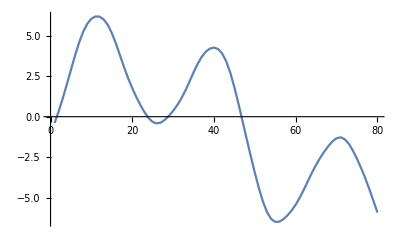

```mathematica
ListLinePlot[Array[tsm,80]]
```

```mathematica
tsm["BestFit"]
```

ARIMAProcess[0.0000610228,{1.6676,-1.19273,0.0167579,0.308378},4,{0.146089},0.0000115323]

```mathematica
tsm["BestFitParameters"]
```

{1.6676,-1.19273,0.0167579,0.308378,0.146089}

```mathematica
tsm["ModelFamily"]
```

ARIMA

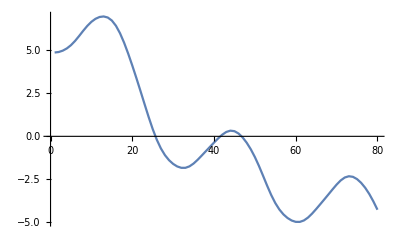

```mathematica
ListLinePlot[reducedOxyNo80[[4,1]]]
```

```mathematica
(#-> TimeSeriesModelFit[reducedOxyNo80[[#,1]]]["ModelFamily"])&/@Range[30]
```

{1→ARIMA,2→SARIMA,3→SARIMA,4→SARIMA,5→ARIMA,6→ARIMA,7→ARIMA,8→SARIMA,9→SARIMA,10→SARIMA,11→SARIMA,12→SARIMA,13→SARIMA,14→SARIMA,15→ARIMA,16→SARIMA,17→ARIMA,18→SARIMA,19→SARIMA,20→SARIMA,21→SARIMA,22→SARIMA,23→SARIMA,24→ARIMA,25→SARIMA,26→SARIMA,27→SARIMA,28→SARIMA,29→SARIMA,30→SARIMA}

```mathematica
Range[30]/.%216
```

{ARIMA,SARIMA,SARIMA,SARIMA,ARIMA,ARIMA,ARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,ARIMA,SARIMA,ARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,ARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA,SARIMA}

```mathematica
Counts[%221]
```

<|ARIMA→7,SARIMA→23|>

```mathematica
coefNoARMA =Table[TimeSeriesModelFit[reducedOxyNo80[[x,1]],"SARIMA"]["BestFitParameters"],{x,30}];
```

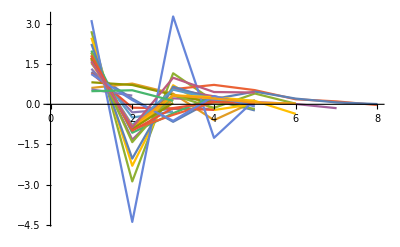

```mathematica
ListLinePlot[coefNoARMA]
```

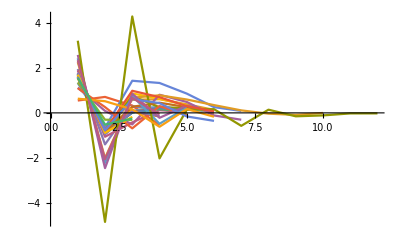

```mathematica
coefYesARMA =Table[TimeSeriesModelFit[reducedOxyYes80[[x,1]],"SARIMA"]["BestFitParameters"],{x,30}];
ListLinePlot[coefYesARMA]
```

```mathematica
Length/@%298
```

{4,1,3,2,2,2,1,3,4,4,1,4,2,4,3,4,4,4,4,4,4,1,4,4,4,4,2,4,1,5}

```mathematica
coefYesSARIMA =Table[TimeSeriesModelFit[reducedOxyYes80[[x,1]],"SARIMA"]["BestFitParameters"],{x,30}];
```